## Выполнение расчетного задания по дисциплине Тепломассообмен в среде Mathematica 14 Студент: Маркаров М.Г. Группа: ТФ-13-22 Задача № 3

#### -Graphics-

#### Введем исходные данные:

```mathematica
d0=UnitConvert[Quantity[420,"Millimeters"],"Meters"];

r0=d0/2;L=UnitConvert[Quantity[38,"Centimeters"],"Meters"];t0=Quantity[600,"DegreesCelsius"];tLiquid=Quantity[18,"DegreesCelsius"];α=Quantity[70,("Watts")/(("Meters")^2*"Kelvins")];
ρ=Quantity[7865,("Kilograms")/("Meters")^3];
cp=Quantity[460,("Joules")/("Kilograms"*"Kelvins")];
λ=Quantity[61,("Watts")/("Meters"*"Kelvins")];
τ1=UnitConvert[Quantity[5.8,"Minutes"],"Seconds"];
```

#### Найдем коэффициент температуропроводности a:

```mathematica
a=UnitConvert[N[λ/(cp*ρ)],("Meters")^2/("Seconds")]
```

0.0000168606 m^2/s

#### Числа Био по радиальному( BiRadial) и вертикальному( BiVertical) направлениям:

```mathematica
BiRadial=N[(α*r0)/λ]
```

0.240984

```mathematica
BiVertical=N[(α*L/2)/λ]
```

0.218033

#### Числа Фурье по радиальному( FoRadial) и вертикальному( FoVertical) направлениям:

```mathematica
FoRadial=(a*τ1)/(r0)^2
```

0.13305

```mathematica
FoVertical=(a*τ1)/(L/2)^2
```

0.162534

#### Приступим к поиску корней характеристического уравнения(MATLAB) в радиальном направлении: -Graphics- Отдельно рассмотрим седьмой корень(определим его визуально с точностью е-4) -Graphics-

```mathematica
ϵ={0.6739,3.8940,7.0498,10.1971,13.3418,16.4853,19.6281};
```

#### В вертикальном направлении: -Graphics- 7 корень: -Graphics-

```mathematica
μ={0.4506  ,  3.2094  ,  6.3177   , 9.4479 ,  12.5837   ,15.7218 ,  18.8611  };
```

#### Найдем функцию распределения температуры в радиальном направлении:

```mathematica
ΘRadial[r_,τ_]:=Total[(2*BesselJ[1,ϵ])/(ϵ*(BesselJ[0,ϵ]+BesselJ[1,ϵ]^2))*BesselJ[0,ϵ*r/QuantityMagnitude[r0]]*Exp[-ϵ^2*QuantityMagnitude[a]*τ/QuantityMagnitude[r0]^2]];
```

```mathematica
ΘRadial[0,0]
```

1.00486

```mathematica
tRadial[r_,τ_]=tLiquid + (t0-tLiquid)*ΘRadial[r,τ];
```

#### Найдем температуру на оси цилиндра в момент времени τ = 0

```mathematica
tRadial[0,0]
```

875.981 K

```mathematica
UnitConvert[tRadial[0,0],"DegreesCelsius"]
```

602.831 °C

#### Найдем функцию распределения температуры в вертикальном направлении:

```mathematica
ΘVertical[x_,τ_]:=Total[(2*Sin[μ])/(μ+Sin[μ]*Cos[μ])*Cos[μ*x/QuantityMagnitude[L/2]]*Exp[-μ^2*(QuantityMagnitude[a]*τ)/QuantityMagnitude[(L/2)^2]]]
```

```mathematica
ΘVertical[0,0]
```

1.00052

```mathematica
tVertical[x_,τ_]:=tLiquid + (t0-tLiquid)*ΘVertical[x,τ];
```

#### Найдем температуру в центре цилиндра в момент времени τ = 0

```mathematica
tVertical[0,0]
```

873.453 K

```mathematica
UnitConvert[tVertical[0,0],"DegreesCelsius"]
```

600.303 °C

#### Найдем функцию распределения температурного поля в цилиндре t(x,r,τ)

```mathematica
Θ3D[x_,r_,τ_]:=ΘVertical[x,τ]*ΘRadial[r,τ];
```

```mathematica
t[x_,r_,τ_]:=tLiquid + (t0-tLiquid)*Θ3D[x,r,τ];
```

#### Начнем расчет температурного поля Сначала для r=0:

```mathematica
Table[{ N[x],UnitConvert[t[QuantityMagnitude[x],QuantityMagnitude[0],QuantityMagnitude[τ1]],"DegreesCelsius"]},{x,{L/2,3*L/8,L/4,L/8,0}}]//MatrixForm
```

(0.19 m | 494.347 °C
0.1425 m | 515.991 °C
0.095 m | 529.518 °C
0.0475 m | 536.497 °C
0. | 538.59 °C)

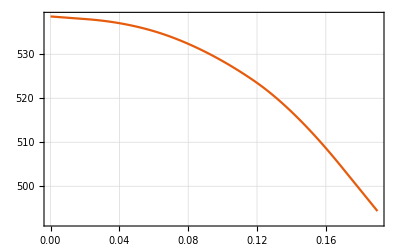

```mathematica
ListLinePlot[Table[{ N[x],UnitConvert[t[QuantityMagnitude[x],QuantityMagnitude[0],QuantityMagnitude[τ1]],"DegreesCelsius"]},{x,{L/2,3*L/8,L/4,L/8,0}}],InterpolationOrder->2,PlotTheme->"Scientific",GridLines->Automatic]
```

#### Теперь для r=r0

```mathematica
Table[{ N[x],UnitConvert[t[QuantityMagnitude[x],QuantityMagnitude[r0],QuantityMagnitude[τ1]],"DegreesCelsius"]},{x,{L/2,3*L/8,L/4,L/8,0}}]//MatrixForm
```

(0.19 m | 438.887 °C
0.1425 m | 458.011 °C
0.095 m | 469.964 °C
0.0475 m | 476.129 °C
0. | 477.979 °C)

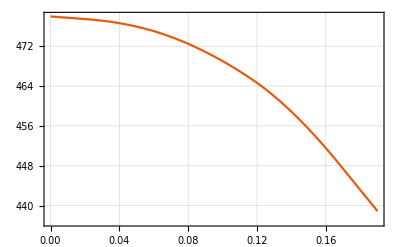

```mathematica
ListLinePlot[Table[{ N[x],UnitConvert[t[QuantityMagnitude[x],QuantityMagnitude[r0],QuantityMagnitude[τ1]],"DegreesCelsius"]},{x,{L/2,3*L/8,L/4,L/8,0}}],InterpolationOrder->2,PlotTheme->"Scientific",GridLines->Automatic]
```

#### Теперь для x=0

```mathematica
Table[{ N[r],UnitConvert[t[QuantityMagnitude[0],QuantityMagnitude[r],QuantityMagnitude[τ1]],"DegreesCelsius"]},{r,Reverse[{0,r0/4,r0/2,3*r0/4,r0}]}]//MatrixForm
```

(0.21 m | 477.979 °C
0.1575 m | 503.005 °C
0.105 m | 522.155 °C
0.0525 m | 534.37 °C
0. | 538.59 °C)

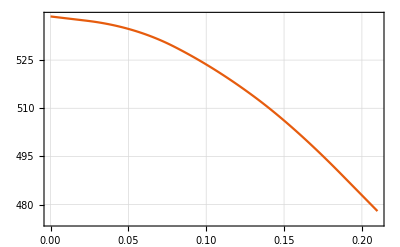

```mathematica
ListLinePlot[Table[{ N[r],UnitConvert[t[QuantityMagnitude[0],QuantityMagnitude[r],QuantityMagnitude[τ1]],"DegreesCelsius"]},{r,Reverse[{0,r0/4,r0/2,3*r0/4,r0}]}],InterpolationOrder->2,PlotTheme->"Scientific",GridLines->Automatic]
```

#### Теперь для x=L/2

```mathematica
Table[{ N[r],UnitConvert[t[QuantityMagnitude[L/2],QuantityMagnitude[r],QuantityMagnitude[τ1]],"DegreesCelsius"]},{r,Reverse[{0,r0/4,r0/2,3*r0/4,r0}]}]//MatrixForm
```

(0.21 m | 438.887 °C
0.1575 m | 461.786 °C
0.105 m | 479.308 °C
0.0525 m | 490.485 °C
0. | 494.347 °C)

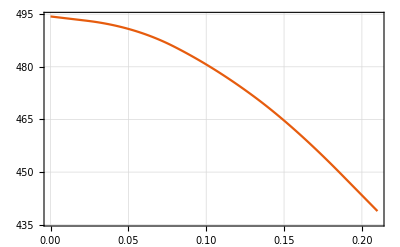

```mathematica
ListLinePlot[Table[{ N[r],UnitConvert[t[QuantityMagnitude[L/2],QuantityMagnitude[r],QuantityMagnitude[τ1]],"DegreesCelsius"]},{r,Reverse[{0,r0/4,r0/2,3*r0/4,r0}]}],InterpolationOrder->2,PlotTheme->"Scientific",GridLines->Automatic]
```

#### Покажем распределение температуры в центре цилиндра и на расстоянии 0.2 d_0 от поверхности как функцию времени Сначала для центра:

```mathematica
Table[{ N[k*τ1],UnitConvert[t[QuantityMagnitude[0],QuantityMagnitude[0],QuantityMagnitude[k*τ1]],"DegreesCelsius"]},{k,Range[10]}]//MatrixForm
```

(348. s | 538.59 °C
696. s | 493.205 °C
1044. s | 451.097 °C
1392. s | 412.528 °C
1740. s | 377.351 °C
2088. s | 345.302 °C
2436. s | 316.109 °C
2784. s | 289.52 °C
3132. s | 265.302 °C
3480. s | 243.245 °C)

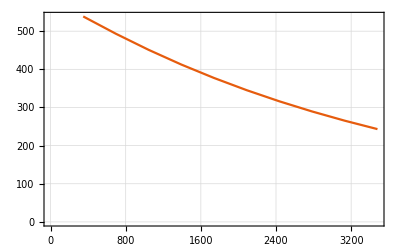

```mathematica
ListLinePlot[Table[{ N[k*τ1],UnitConvert[t[QuantityMagnitude[0],QuantityMagnitude[0],QuantityMagnitude[k*τ1]],"DegreesCelsius"]},{k,Range[10]}],PlotTheme->"Scientific",GridLines->Automatic]
```

#### Теперь на расстоянии 0.2 d_0 (0.4 r_0)от поверхности , следовательно r=0.6 r_0)

```mathematica
Table[{ N[k*τ1],UnitConvert[t[QuantityMagnitude[0],QuantityMagnitude[0.6*r0],QuantityMagnitude[k*τ1]],"DegreesCelsius"]},{k,Range[10]}]//MatrixForm
```

(348. s | 515.261 °C
696. s | 473.687 °C
1044. s | 433.537 °C
1392. s | 396.562 °C
1740. s | 362.812 °C
2088. s | 332.06 °C
2436. s | 304.049 °C
2784. s | 278.535 °C
3132. s | 255.297 °C
3480. s | 234.132 °C)

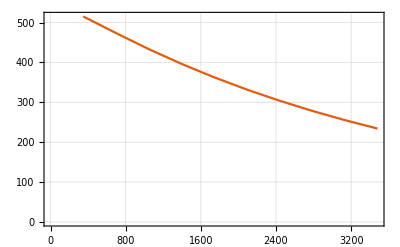

```mathematica
ListLinePlot[Table[{ N[k*τ1],UnitConvert[t[QuantityMagnitude[0],QuantityMagnitude[0.6*r0],QuantityMagnitude[k*τ1]],"DegreesCelsius"]},{k,Range[10]}],PlotTheme->"Scientific",GridLines->Automatic]
```

#### Для определения темпа охлаждения и коэффициента температуропроводности заготовки построит несколько зависимостей ln(θ) используя данные полученные выше( в центре и на 0.6r_0). θ = t-tLiquid

```mathematica
lnForCenter=Table[{ N[k*τ1],Log[QuantityMagnitude[UnitConvert[t[QuantityMagnitude[0],QuantityMagnitude[0],QuantityMagnitude[k*τ1]],"DegreesCelsius"]-tLiquid]]},{k,Range[10]}]
```

{{348. s,6.25496},{696. s,6.16375},{1044. s,6.07096},{1392. s,5.97769},{1740. s,5.8843},{2088. s,5.79088},{2436. s,5.69746},{2784. s,5.60404},{3132. s,5.51061},{3480. s,5.41719}}

```mathematica
lnForPoint6r0=Table[{ N[k*τ1],Log[QuantityMagnitude[UnitConvert[t[QuantityMagnitude[0],QuantityMagnitude[0.6*r0],QuantityMagnitude[k*τ1]],"DegreesCelsius"]-tLiquid]]},{k,Range[10]}]
```

{{348. s,6.20912},{696. s,6.12181},{1044. s,6.02957},{1392. s,5.93638},{1740. s,5.843},{2088. s,5.74958},{2436. s,5.65616},{2784. s,5.56274},{3132. s,5.46931},{3480. s,5.37589}}

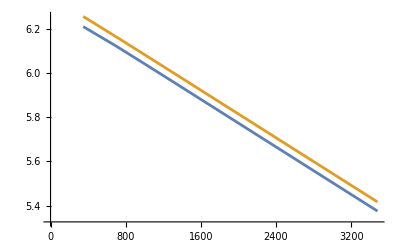

```mathematica
ListLinePlot[{lnForPoint6r0,lnForCenter}]
```

#### Нетрудно заметить,что стадии регулярного режима гарантированно соответствует интервал [1000,2500] s. Найдем число Фурье в краевых точках интервала регулярного режима и удостоверимся что оно больше 0.3

```mathematica
FoRadialAt1000=(a*Quantity[1000,"Seconds"])/r0^2
```

0.382327

```mathematica
FoRadialAt2500=(a*Quantity[2500,"Seconds"])/r0^2
```

0.955817

```mathematica
FoVerticalAt1000=(a*Quantity[1000,"Seconds"])/(L/2)^2
```

0.467053

```mathematica
FoVerticalAt2500=(a*Quantity[2500,"Seconds"])/(L/2)^2
```

1.16763

#### Приступим к поиску темпа охлаждения m для наших двух точек

```mathematica
mAtCenter=Log[Θ3D[0,0,1000]/Θ3D[0,0,2500]]/Quantity[2500-1000,"Seconds"]
```

0.000268303 per second

```mathematica
mAtPoint6r0=Log[Θ3D[0,QuantityMagnitude[0.6*r0],1000]/Θ3D[0,QuantityMagnitude[0.6*r0],2500]]/Quantity[2500-1000,"Seconds"]
```

0.000268225 per second

#### Берем среднее

```mathematica
m=(mAtCenter+mAtPoint6r0)/2
```

0.000268264 per second

#### Fo > 0.3 поэтому ряд Фурье сходится быстро и первый член достаточно описывает все решение. Найдем коэффициент формы K:

```mathematica
K=1/((First[ϵ]/r0)^2+(First[μ]/(L/2))^2)
```

0.0628047 m^2

#### Найдем коэффициент температуропроводности по второй теореме Кондратьева(допущение что наше m=m_∞) и сравним с теоретическим:

```mathematica
aExperimental=K*m
```

0.0000168482 m^2/s

```mathematica
a
```

0.0000168606 m^2/s

```mathematica
δa=Abs[a-aExperimental]/a
```

0.000733348

#### Найдем количество теплоты, отданное цилиндром за время τ_1: Для начала найдем сколько теплоты он отдаст до того момента как Θ==1 т.е. t=tLiquid

```mathematica
Q=N[π*(r0)^2*L*ρ*cp*(t0-tLiquid)]
```

1.10854×10^8 J

```mathematica
ΘRadialAverage=Total[(4*BiRadial^2)/(ϵ^2*(ϵ^2+BiRadial^2))*Exp[-ϵ^2*FoRadial]]
```

0.940184

```mathematica
ΘVerticalAverage=Total[(2*Sin[μ]^2)/(μ^2+μ*Sin[μ]*Cos[μ])*Exp[-μ^2*FoVertical]]
```

0.96678

```mathematica
ΘAverage=ΘVerticalAverage*ΘRadialAverage
```

0.908951

```mathematica
Qτ1=Q(1-ΘAverage)
```

1.00931×10^7 J

#### Подытожим полным температурным полем в момент времени τ_1

```mathematica
Show[ListLinePlot3D[Table[t[QuantityMagnitude[x],QuantityMagnitude[r],QuantityMagnitude[τ1]],{x,0,L/2,L/4},{r,0,r0,r0/4}]],Boxed->False]
```

-Graphics3D-

```mathematica
data=Flatten[Table[{x,r,t[QuantityMagnitude[x],QuantityMagnitude[r],QuantityMagnitude[τ1]]},{x,0,L/2,L/4},{r,0,r0,r0/4}],1];

ListPlot3D[data,Boxed->True,Mesh->None,PlotStyle->Directive[Opacity[0.7],Yellow],AxesLabel->{"x (m)","r (m)","t (°C)"},LabelStyle->Directive[Medium,Black],InterpolationOrder->4]
```

-Graphics3D-